## Import the Audio File

```mathematica
whisperDBSPL = 25
```

25

```mathematica
normalConversationDBSPL = 70
```

70

```mathematica
DBSPLDeltaSensitivity = 0.4
```

0.4

NB Don' t forget to apply sound masking curves to decide whether certain spikeyness is dicernible or not

```mathematica
utterance =Import["~/workspace/gnu-radio/recordings/6_5_2.wav"]
```

-Graphics-

```mathematica
fred = Head@First@utterance
```

SampledSoundList

```mathematica
Length@utterance[[1,1,1]]
```

220500

```mathematica
sampleChunk = Take[utterance[[1,1,1]], {70000, 75000}]
```

{-0.0212097,-0.00942993,-0.010437,-0.00119019,0.00140381,-0.0065918,-0.0119629,4987,0.0491333,0.0492554,0.0423279,0.0423279,0.0404663,0.0274963,0.0295715}
 |  |  |  |

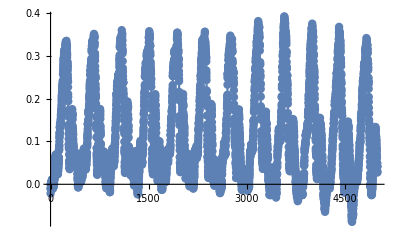

```mathematica
ListLinePlot[sampleChunk,Mesh->All]
```

```mathematica
Round[Length[sampleChunk]/12]
```

417

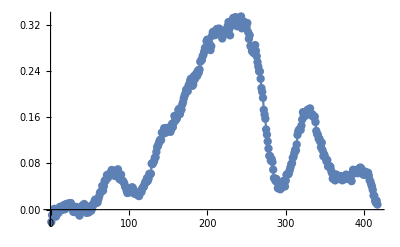

```mathematica
ListLinePlot[Take[sampleChunk, Round[Length[sampleChunk]/12]],Mesh->All]
```

```mathematica
spikey1 = Partition[sampleChunk, 4]
```

{{-0.0212097,-0.00942993,-0.010437,-0.00119019},{0.00140381,-0.0065918,-0.0119629,-0.0022583},1247,{0.0423279,0.0423279,0.0404663,0.0274963}}
 |  |  |  |

```mathematica
Abs@{2.3, -5}
```

{2.3,5}

## Establish Formulas For Computing Spikes And Graphing them

```mathematica
KochSpikeVal[list_] := If[Abs[(list[[1]]+list[[4]])] > 0,(list[[2]]+list[[3]])/(list[[1]]+list[[4]]), (list[[2]]+list[[3]])]
```

```mathematica
KochSpikeAbsVal[list_] := KochSpikeVal[Abs@list]
```

```mathematica
KochSpikeVal[{1,2,3,4}]
```

1

```mathematica
spikeyAllVal= NestWhileList[Map[KochSpikeVal,  Partition[#, 4]]&, sampleChunk, Length[#]>1&]
```

{1}
 |  |  |  |

```mathematica
spikeyAllAbs= NestWhileList[Map[KochSpikeAbsVal,  Partition[#, 4]]&, sampleChunk, Length[#]>1&]
```

{{-0.0212097,-0.00942993,-0.010437,-0.00119019,0.00140381,-0.0065918,-0.0119629,4988,0.0492554,0.0423279,0.0423279,0.0404663,0.0274963,0.0295715},6}
 |  |  |  |

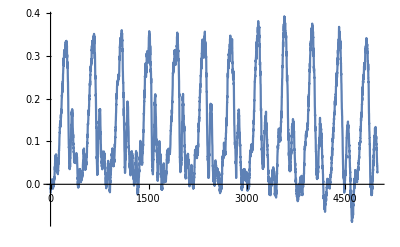
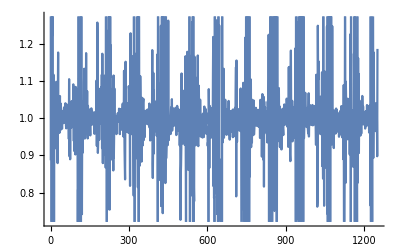
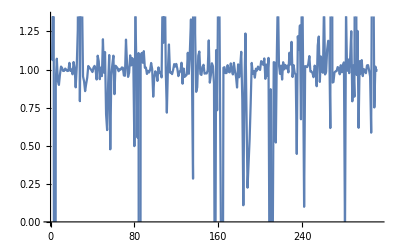
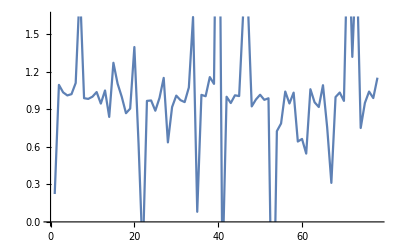
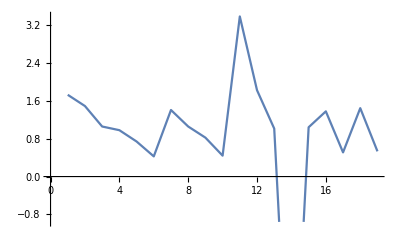
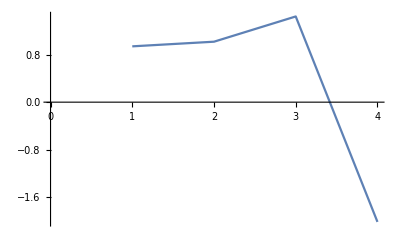
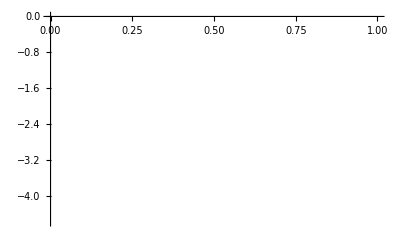
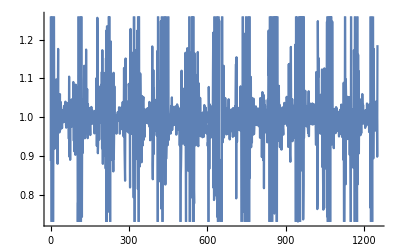
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
 |  |  |  |

```mathematica
Map[Map[ListLinePlot, #]&, {spikeyAllVal,spikeyAllAbs}]
```

Now run the Koch Spike mapping on all the wav file

```mathematica
spikeyUttVal= NestWhileList[Map[KochSpikeVal,  Partition[#, 4]]&, utterance[[1,1,1]], Length[#]>1&]
```

{{-0.00238037,0.0100098,0.00335693,-0.00247192,0.00753784,-0.00219727,-0.00244141,220487,-0.00799561,-0.00823975,-0.0111084,-0.00872803,-0.00534058,-0.0085144},8,{}}
 |  |  |  |

```mathematica
spikeyUttAbsVal= NestWhileList[Map[KochSpikeAbsVal,  Partition[#, 4]]&, utterance[[1,1,1]], Length[#]>1&]
```

{{-0.00238037,0.0100098,0.00335693,-0.00247192,0.00753784,-0.00219727,-0.00244141,220487,-0.00799561,-0.00823975,-0.0111084,-0.00872803,-0.00534058,-0.0085144},8,{}}
 |  |  |  |

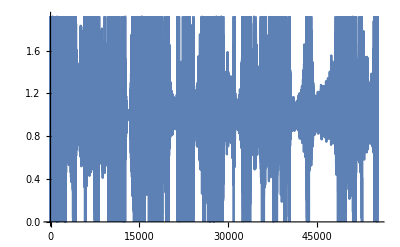
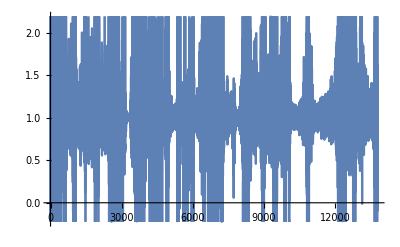
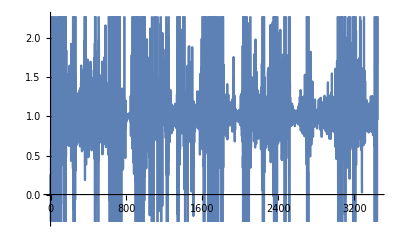
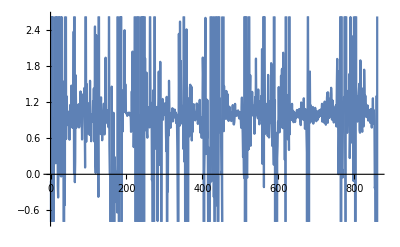
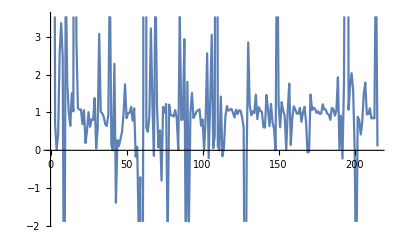
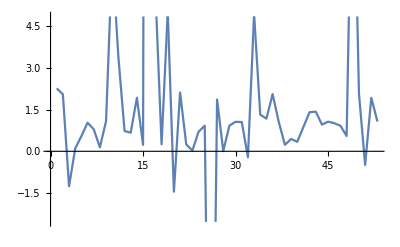
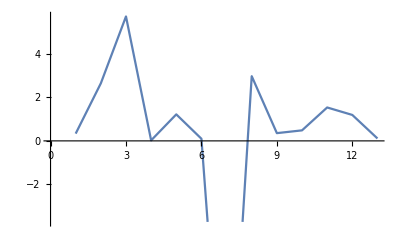
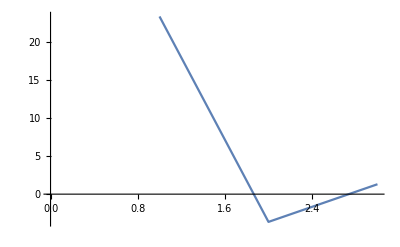
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
 |  |  |  |

```mathematica
Map[Map[ListLinePlot, #]&, {spikeyUttVal,spikeyUttAbsVal}]
```

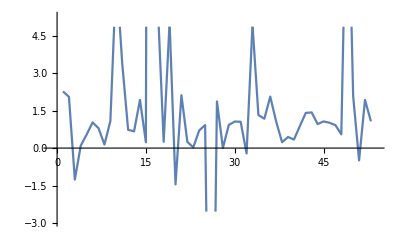

## Now Do it properly

We missed the first step of finding the deltas and instead calculated spikiness using values which means nothing realy

```mathematica
deltas = Map[Apply[Subtract, #]&,  Partition[#, 2]]&
```

(Subtract@@#1&)/@Partition[#1,2]&
 |  |  |  |

```mathematica
deltas@sampleChunk
```

{-0.0117798,-0.00924683,0.00799561,-0.00970459,0.00210571,-0.00323486,0.00463867,2486,0.00534058,0.00704956,0.00549316,0.0111389,-0.00012207,0.,0.01297}
 |  |  |  |

```mathematica
spikeyUttVal= NestWhileList[Map[KochSpikeVal,  Partition[#, 4]]&, deltas@utterance[[1,1,1]], Length[#]>1&]
```

{{-0.0123901,0.00582886,0.00973511,-0.00567627,0.00415039,0.000732422,-0.00485229,0.00430298,0.00161743,0.00479126,-0.000213623,0.00491333,-0.000793457,-0.00561523,110222,-0.00234985,0.00405884,-0.00143433,-0.000396729,-0.00338745,0.00262451,0.00350952,-0.00543213,0.00088501,-0.00311279,-0.00158691,0.000244141,-0.00238037,0.00317383},7,{-8.39481}}
 |  |  |  |

```mathematica
spikeyUttAbs= NestWhileList[Map[KochSpikeAbsVal,  Partition[#, 4]]&, deltas@utterance[[1,1,1]], Length[#]>1&]
```

{1}
 |  |  |  |

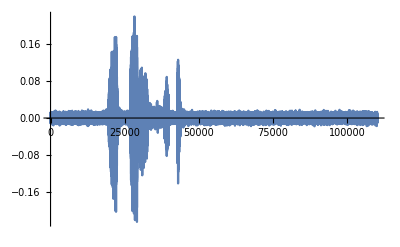
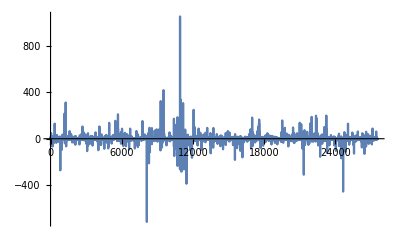
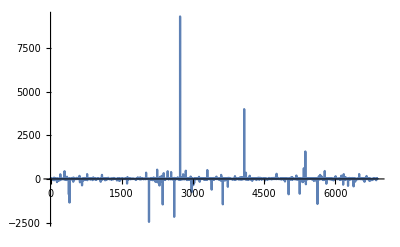
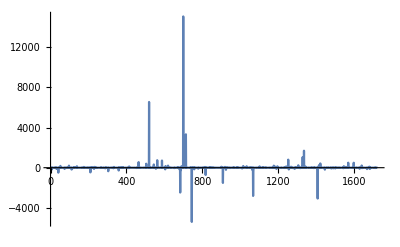
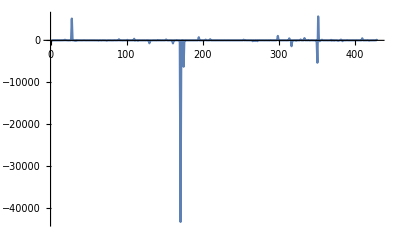
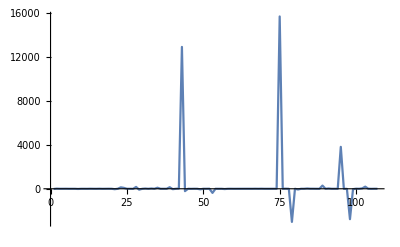
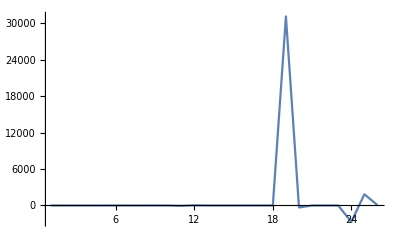
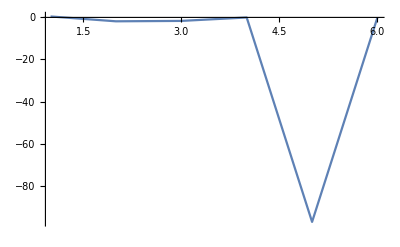
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
 |  |  |  |

```mathematica
Map[Map[ListLinePlot[#, PlotRange->All]&, #]&, {spikeyUttVal,spikeyUttAbs}]
```

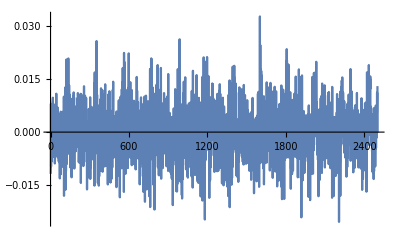

```mathematica
ListLinePlot[deltas@sampleChunk]
```

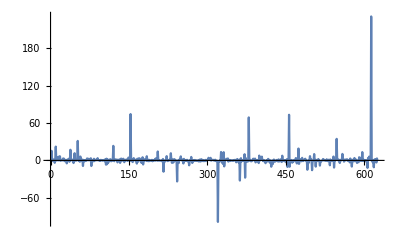
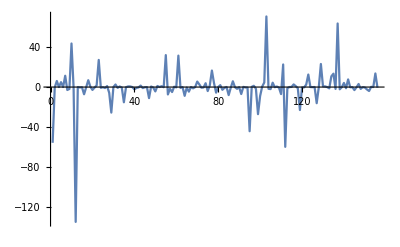
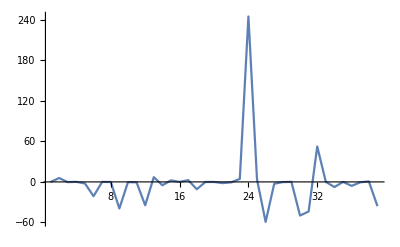
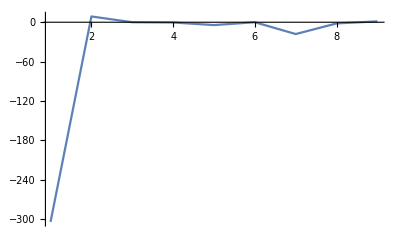
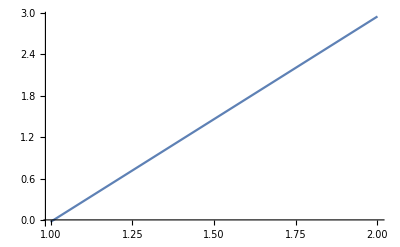
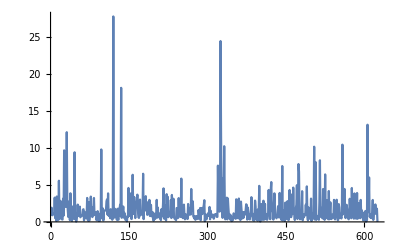
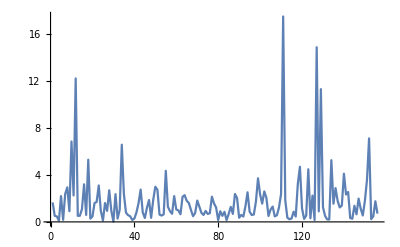
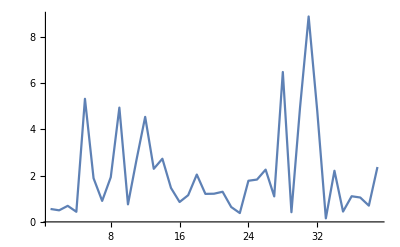
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
 |  |  |  |

```mathematica
Map[Map[ListLinePlot[#, PlotRange->All]&, #]&, {
NestWhileList[Map[KochSpikeVal,  Partition[#, 4]]&, deltas@sampleChunk, Length[#]>1&],
NestWhileList[Map[KochSpikeAbsVal,  Partition[#, 4]]&, deltas@sampleChunk, Length[#]>1&]
}]
```

## Now Test it with different spoken utterances

We might see some invariane charachteristics when utterances contain share Phones

```mathematica
utt652 =Import["~/workspace/gnu-radio/recordings/6_5_2.wav"]
```

-Graphics-

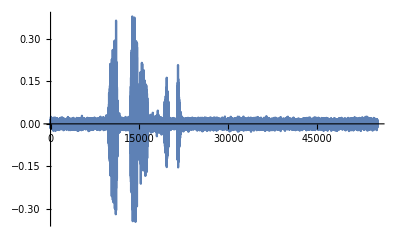
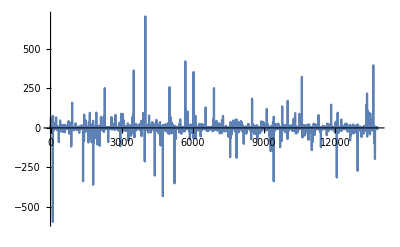
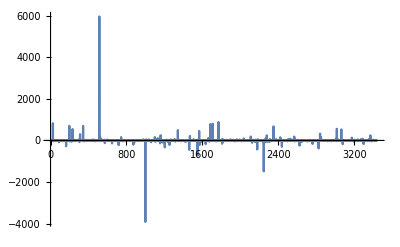
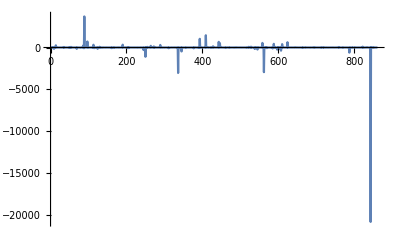
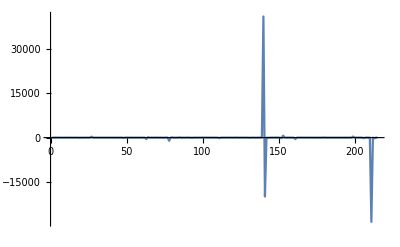
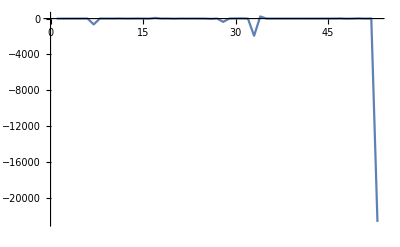
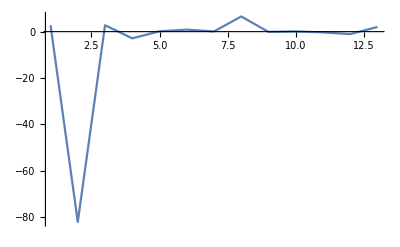
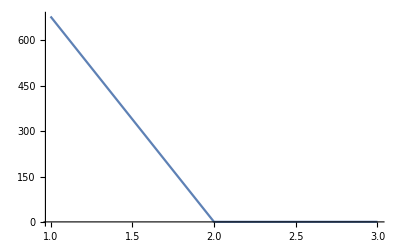
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
 |  |  |  |

```mathematica
Map[Map[ListLinePlot[#, PlotRange->All]&, #]&, {
NestWhileList[Map[KochSpikeVal,  Partition[#, 4]]&, deltas@deltas@utt652[[1,1,1]], Length[#]>1&],
NestWhileList[Map[KochSpikeAbsVal,  Partition[#, 4]]&, deltas@utt652[[1,1,1]], Length[#]>1&]
}]
```

```mathematica
utt286 =Import["~/workspace/gnu-radio/recordings/2_8_6.wav"]
```

-Graphics-

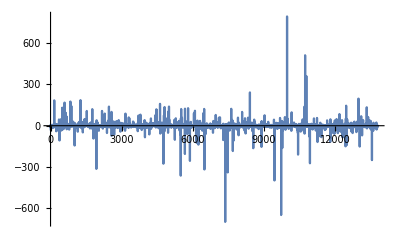
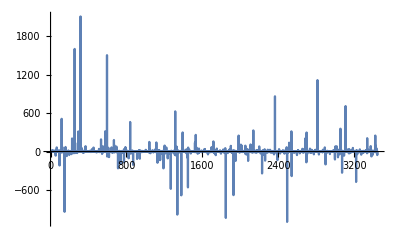
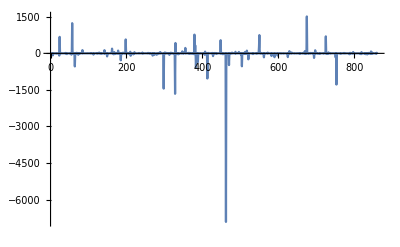
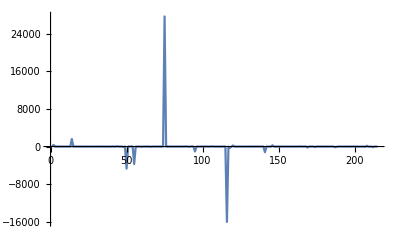
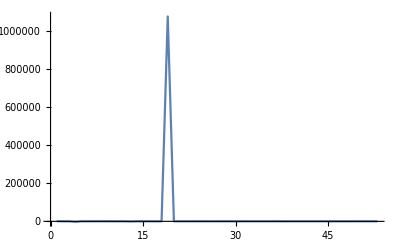
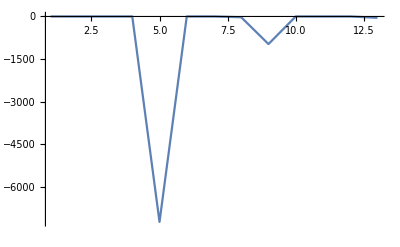
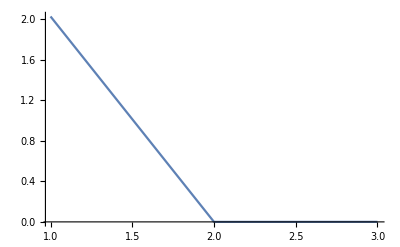
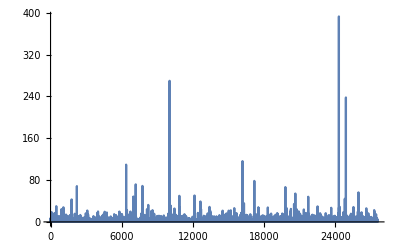
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
 |  |  |  |

```mathematica
Map[Map[ListLinePlot[#, PlotRange->All]&, #]&, {
NestWhileList[Map[KochSpikeVal,  Partition[#, 4]]&, deltas@deltas@utt286[[1,1,1]], Length[#]>1&],
NestWhileList[Map[KochSpikeAbsVal,  Partition[#, 4]]&, deltas@utt286[[1,1,1]], Length[#]>1&]
}]
```

```mathematica
utt354 =Import["~/workspace/gnu-radio/recordings/3_5_4.wav"]
```

-Graphics-

```mathematica
utt135 =Import["~/workspace/gnu-radio/recordings/1_3_5.wav"]
```

-Graphics-

{-0.00238037,0.0100098,0.00335693,-0.00247192,0.00753784,-0.00219727,-0.00244141,220486,-0.010498,-0.00799561,-0.00823975,-0.0111084,-0.00872803,-0.00534058,-0.0085144}
 |  |  |  |

```mathematica
g286 =-Graphics-
```

-Graphics-

```mathematica
g652 = -Graphics-
```

-Graphics-

```mathematica
g286Val1 =-Graphics-
```

-Graphics-

```mathematica
g286Abs1 = -Graphics-
```

-Graphics-

```mathematica
g652Val1 = -Graphics-
```

-Graphics-

```mathematica
g652Abs1 = -Graphics-
```

-Graphics-